# LINQ does the Teapot

```mathematica
teapotOFF={format->"OFF",nvertices->480,nfaces->448,nedges->926, vertices->{{0,0,0.488037},{0.00390625,0.0421881,0.476326},{0.00390625,-0.0421881,0.476326},{0.0107422,0,0.575333},{0.0125,0.0562508,0.450561},{0.0125,-0.0562508,0.450561},{0.0195312,0,0.413654},{0.0210938,0.0421881,0.424797},{0.0210938,-0.0421881,0.424797},{0.025,0,0.413086},{0.03875,0.19625,0.488037},{0.03875,-0.19625,0.488037},{0.0390625,0,0.66803},{0.0486597,0.192034,0.575333},{0.0486597,-0.192034,0.575333},{0.0567676,0.188584,0.413654},{0.0567676,-0.188584,0.413654},{0.0625,0,0.358795},{0.0747852,0.180918,0.66803},{0.0747852,-0.180918,0.66803},{0.0791016,0,0.764481},{0.0964063,0.171719,0.358795},{0.0964063,-0.171719,0.358795},{0.1,0,0.769043},{0.103906,0.0421881,0.777779},{0.103906,-0.0421881,0.777779},{0.105469,0,0.32156},{0.111721,0.165203,0.764481},{0.111721,-0.165203,0.764481},{0.1125,0.0562508,0.796997},{0.1125,-0.0562508,0.796997},{0.121094,0.0421881,0.816215},{0.121094,-0.0421881,0.816215},{0.125,0,0.300049},{0.125,0,0.824951},{0.125,0,0.863037},{0.136045,0.154853,0.32156},{0.136045,-0.154853,0.32156},{0.137695,0,0.881027},{0.145,0.355,0.488037},{0.145,-0.355,0.488037},{0.149219,0,0.887024},{0.15,0,0.863037},{0.152627,0.347373,0.575333},{0.152627,-0.347373,0.575333},{0.154062,0.147187,0.300049},{0.154062,0.147187,0.863037},{0.154062,-0.147187,0.300049},{0.154062,-0.147187,0.863037},{0.154883,0,0.881027},{0.158867,0.341133,0.413654},{0.158867,-0.341133,0.413654},{0.165774,0.142205,0.881027},{0.165774,-0.142204,0.881027},{0.172734,0.327266,0.66803},{0.172734,-0.327266,0.66803},{0.175,0,0.863037},{0.176404,0.137682,0.887024},{0.176404,-0.137681,0.887024},{0.177125,0.137375,0.863037},{0.177125,-0.137375,0.863037},{0.181629,0.135459,0.881027},{0.181629,-0.135458,0.881027},{0.189375,0.310625,0.358795},{0.189375,-0.310625,0.358795},{0.200187,0.127562,0.863037},{0.200187,-0.127562,0.863037},{0.201162,0.298838,0.764481},{0.201162,-0.298838,0.764481},{0.210938,0,0.884945},{0.219883,0.280117,0.32156},{0.219883,-0.280117,0.32156},{0.23334,0.113457,0.884945},{0.23334,-0.113457,0.884945},{0.23375,0.26625,0.300049},{0.23375,0.26625,0.863037},{0.23375,-0.26625,0.300049},{0.23375,-0.26625,0.863037},{0.242764,0.257238,0.881027},{0.242764,-0.257235,0.881027},{0.250945,0.249056,0.887024},{0.250945,-0.249054,0.887024},{0.2515,0.2485,0.863037},{0.2515,-0.2485,0.863037},{0.254967,0.245034,0.881027},{0.254967,-0.245033,0.881027},{0.26925,0.23075,0.863037},{0.26925,-0.23075,0.863037},{0.29375,0,0.900055},{0.294766,0.205234,0.884945},{0.294766,-0.205234,0.884945},{0.30375,0.46125,0.488037},{0.30375,-0.46125,0.488037},{0.307966,0.45134,0.575333},{0.307966,-0.45134,0.575333},{0.309734,0.080953,0.900055},{0.309734,-0.080953,0.900055},{0.311416,0.443233,0.413654},{0.311416,-0.443233,0.413654},{0.319082,0.425215,0.66803},{0.319082,-0.425215,0.66803},{0.328281,0.403594,0.358795},{0.328281,-0.403594,0.358795},{0.334797,0.388279,0.764481},{0.334797,-0.388279,0.764481},{0.345146,0.363955,0.32156},{0.345146,-0.363955,0.32156},{0.352812,0.345937,0.300049},{0.352812,0.345937,0.863037},{0.352812,-0.345937,0.300049},{0.352812,-0.345937,0.863037},{0.353562,0.146438,0.900055},{0.353562,-0.146438,0.900055},{0.357795,0.334229,0.881027},{0.357795,-0.334224,0.881027},{0.362318,0.323599,0.887024},{0.362318,-0.323595,0.887024},{0.362625,0.322875,0.863037},{0.362625,-0.322875,0.863037},{0.364542,0.318373,0.881027},{0.364542,-0.318371,0.881027},{0.372437,0.299813,0.863037},{0.372437,-0.299813,0.863037},{0.385938,0,0.915394},{0.386543,0.266661,0.884945},{0.386543,-0.266661,0.884945},{0.394777,0.0447694,0.915394},{0.394777,-0.0447694,0.915394},{0.414844,0,1.03776},{0.41875,0,1.00793},{0.419016,0.0809842,0.915394},{0.419016,-0.0809842,0.915394},{0.419047,0.190266,0.900055},{0.419047,-0.190266,0.900055},{0.421414,0.0335127,1.03776},{0.421414,-0.0335127,1.03776},{0.425021,0.0319696,1.00793},{0.425021,-0.0319696,1.00793},{0.43946,0.0605401,1.03776},{0.43946,-0.0605401,1.03776},{0.442242,0.0577578,1.00793},{0.442242,-0.0577578,1.00793},{0.45,0,0.937988},{0.450781,0,0.971153},{0.453875,0.0196248,0.937988},{0.453875,-0.0196248,0.937988},{0.454586,0.0193479,0.971153},{0.454586,-0.0193479,0.971153},{0.45523,0.105222,0.915394},{0.45523,-0.105222,0.915394},{0.4645,0.0354995,0.937988},{0.4645,-0.0354995,0.937988},{0.465028,0.0349715,0.971153},{0.465028,-0.0349715,0.971153},{0.466487,0.0785866,1.03776},{0.466487,-0.0785866,1.03776},{0.46803,0.0749796,1.00793},{0.46803,-0.0749796,1.00793},{0.480375,0.0461242,0.937988},{0.480375,-0.0461242,0.937988},{0.480652,0.0454139,0.971153},{0.480652,-0.0454139,0.971153},{0.5,0,1.05005},{0.5,0.0492185,0.971153},{0.5,0.049999,0.937988},{0.5,0.0812503,1.00793},{0.5,0.0851567,1.03776},{0.5,0.114062,0.915394},{0.5,0.20625,0.900055},{0.5,0.289063,0.884945},{0.5,0.325001,0.863037},{0.5,0.34512,0.881027},{0.5,0.35,0.863037},{0.5,0.350785,0.887024},{0.5,0.362308,0.881027},{0.5,0.375,0.300049},{0.5,0.375,0.863037},{0.5,0.394531,0.32156},{0.5,0.420898,0.764481},{0.5,0.4375,0.358795},{0.5,0.460938,0.66803},{0.5,0.480469,0.413654},{0.5,0.489258,0.575333},{0.5,0.5,0.488037},{0.5,-0.0492185,0.971153},{0.5,-0.049999,0.937988},{0.5,-0.0812503,1.00793},{0.5,-0.0851567,1.03776},{0.5,-0.114062,0.915394},{0.5,-0.20625,0.900055},{0.5,-0.289063,0.884945},{0.5,-0.325001,0.863037},{0.5,-0.345118,0.881027},{0.5,-0.35,0.863037},{0.5,-0.35078,0.887024},{0.5,-0.362303,0.881027},{0.5,-0.375,0.300049},{0.5,-0.375,0.863037},{0.5,-0.394531,0.32156},{0.5,-0.420898,0.764481},{0.5,-0.4375,0.358795},{0.5,-0.460938,0.66803},{0.5,-0.480469,0.413654},{0.5,-0.489258,0.575333},{0.5,-0.5,0.488037},{0.519348,0.0454139,0.971153},{0.519348,-0.0454139,0.971153},{0.519625,0.0461242,0.937988},{0.519625,-0.0461242,0.937988},{0.53197,0.0749796,1.00793},{0.53197,-0.0749796,1.00793},{0.533513,0.0785866,1.03776},{0.533513,-0.0785866,1.03776},{0.534972,0.0349715,0.971153},{0.534972,-0.0349715,0.971153},{0.5355,0.0354995,0.937988},{0.5355,-0.0354995,0.937988},{0.54477,0.105222,0.915394},{0.54477,-0.105222,0.915394},{0.545414,0.0193479,0.971153},{0.545414,-0.0193479,0.971153},{0.546125,0.0196248,0.937988},{0.546125,-0.0196248,0.937988},{0.549219,0,0.971153},{0.55,0,0.937988},{0.557758,0.0577578,1.00793},{0.557758,-0.0577578,1.00793},{0.56054,0.0605401,1.03776},{0.56054,-0.0605401,1.03776},{0.574979,0.0319696,1.00793},{0.574979,-0.0319696,1.00793},{0.578586,0.0335127,1.03776},{0.578586,-0.0335127,1.03776},{0.580953,0.190266,0.900055},{0.580953,-0.190266,0.900055},{0.580984,0.0809842,0.915394},{0.580984,-0.0809842,0.915394},{0.58125,0,1.00793},{0.585156,0,1.03776},{0.605223,0.0447694,0.915394},{0.605223,-0.0447694,0.915394},{0.613457,0.266661,0.884945},{0.613457,-0.266661,0.884945},{0.614062,0,0.915394},{0.627562,0.299813,0.863037},{0.627562,-0.299813,0.863037},{0.635459,0.318373,0.881027},{0.635459,-0.318371,0.881027},{0.637375,0.322875,0.863037},{0.637375,-0.322875,0.863037},{0.637682,0.323599,0.887024},{0.637682,-0.323595,0.887024},{0.642205,0.334229,0.881027},{0.642205,-0.334224,0.881027},{0.646437,0.146438,0.900055},{0.646437,-0.146438,0.900055},{0.647187,0.345937,0.300049},{0.647187,0.345937,0.863037},{0.647187,-0.345937,0.300049},{0.647187,-0.345937,0.863037},{0.654853,0.363955,0.32156},{0.654853,-0.363955,0.32156},{0.665203,0.388279,0.764481},{0.665203,-0.388279,0.764481},{0.671719,0.403594,0.358795},{0.671719,-0.403594,0.358795},{0.680918,0.425215,0.66803},{0.680918,-0.425215,0.66803},{0.688584,0.443233,0.413654},{0.688584,-0.443233,0.413654},{0.690266,0.080953,0.900055},{0.690266,-0.080953,0.900055},{0.692034,0.45134,0.575333},{0.692034,-0.45134,0.575333},{0.69625,0.46125,0.488037},{0.69625,-0.46125,0.488037},{0.705234,0.205234,0.884945},{0.705234,-0.205234,0.884945},{0.70625,0,0.900055},{0.73075,0.23075,0.863037},{0.73075,-0.23075,0.863037},{0.745033,0.245034,0.881027},{0.745033,-0.245033,0.881027},{0.7485,0.2485,0.863037},{0.7485,-0.2485,0.863037},{0.749055,0.249056,0.887024},{0.749055,-0.249054,0.887024},{0.757236,0.257238,0.881027},{0.757236,-0.257235,0.881027},{0.76625,0.26625,0.300049},{0.76625,0.26625,0.863037},{0.76625,-0.26625,0.300049},{0.76625,-0.26625,0.863037},{0.76666,0.113457,0.884945},{0.76666,-0.113457,0.884945},{0.780117,0.280117,0.32156},{0.780117,-0.280117,0.32156},{0.789062,0,0.884945},{0.798838,0.298838,0.764481},{0.798838,-0.298838,0.764481},{0.799812,0.127562,0.863037},{0.799812,-0.127562,0.863037},{0.810625,0.310625,0.358795},{0.810625,-0.310625,0.358795},{0.818371,0.135459,0.881027},{0.818371,-0.135458,0.881027},{0.822875,0.137375,0.863037},{0.822875,-0.137375,0.863037},{0.823596,0.137682,0.887024},{0.823596,-0.137681,0.887024},{0.825,0,0.863037},{0.827266,0.327266,0.66803},{0.827266,-0.327266,0.66803},{0.834226,0.142205,0.881027},{0.834226,-0.142204,0.881027},{0.841133,0.341133,0.413654},{0.841133,-0.341133,0.413654},{0.845117,0,0.881027},{0.845937,0.147187,0.300049},{0.845937,0.147187,0.863037},{0.845937,-0.147187,0.300049},{0.845937,-0.147187,0.863037},{0.847373,0.347373,0.575333},{0.847373,-0.347373,0.575333},{0.85,0,0.863037},{0.850781,0,0.887024},{0.855,0.355,0.488037},{0.855,-0.355,0.488037},{0.862305,0,0.881027},{0.863955,0.154853,0.32156},{0.863955,-0.154853,0.32156},{0.875,0,0.300049},{0.875,0,0.863037},{0.888279,0.165203,0.764481},{0.888279,-0.165203,0.764481},{0.894531,0,0.32156},{0.903594,0.171719,0.358795},{0.903594,-0.171719,0.358795},{0.920898,0,0.764481},{0.925,0,0.413086},{0.925,0,0.618896},{0.925,0.0928131,0.445244},{0.925,0.0928131,0.586738},{0.925,0.123751,0.515991},{0.925,-0.0928131,0.445244},{0.925,-0.0928131,0.586738},{0.925,-0.123751,0.515991},{0.925215,0.180918,0.66803},{0.925215,-0.180918,0.66803},{0.9375,0,0.358795},{0.943232,0.188584,0.413654},{0.943232,-0.188584,0.413654},{0.95134,0.192034,0.575333},{0.95134,-0.192034,0.575333},{0.960938,0,0.66803},{0.96125,0.19625,0.488037},{0.96125,-0.19625,0.488037},{0.980469,0,0.413654},{0.989258,0,0.575333},{1,0,0.488037},{1.04492,0,0.646503},{1.05408,0.0838042,0.622637},{1.05408,-0.0838042,0.622637},{1.07422,0.111739,0.570131},{1.07422,-0.111739,0.570131},{1.09436,0.0838042,0.517625},{1.09436,-0.0838042,0.517625},{1.09687,0,0.71286},{1.10352,0,0.493759},{1.10859,0.0639847,0.698941},{1.10859,-0.0639847,0.698941},{1.12539,0,0.79327},{1.13437,0.0853129,0.66832},{1.13437,-0.0853129,0.66832},{1.13967,0.0441651,0.788218},{1.13967,-0.0441651,0.788218},{1.16016,0.0639847,0.637698},{1.16016,-0.0639847,0.637698},{1.17109,0.0588868,0.777105},{1.17109,-0.0588868,0.777105},{1.17188,0,0.623779},{1.175,0,0.863037},{1.19297,0,0.8732},{1.19844,0.0351562,0.863037},{1.19844,-0.0351562,0.863037},{1.2,0,0.863037},{1.20251,0.0441651,0.765992},{1.20251,-0.0441651,0.765992},{1.20625,0,0.876587},{1.21016,0,0.8732},{1.21563,0.0210938,0.863037},{1.21563,-0.0210938,0.863037},{1.2168,0,0.76094},{1.21807,0.032959,0.873741},{1.21807,-0.032959,0.873741},{1.22981,0.028125,0.87746},{1.22981,-0.028125,0.87746},{1.23016,0.023291,0.873967},{1.23016,-0.023291,0.873967},{1.25,0.028125,0.863037},{1.25,0.046875,0.863037},{1.25,-0.028125,0.863037},{1.25,-0.046875,0.863037},{1.27329,0.0439453,0.874933},{1.27329,-0.0439453,0.874933},{1.27417,0.0310547,0.875654},{1.27417,-0.0310547,0.875654},{1.28164,0.0375,0.879379},{1.28164,-0.0375,0.879379},{1.28437,0.0210938,0.863037},{1.28437,-0.0210938,0.863037},{1.3,0,0.863037},{1.30156,0.0351562,0.863037},{1.30156,-0.0351562,0.863037},{1.31818,0.023291,0.877342},{1.31818,-0.023291,0.877342},{1.325,0,0.863037},{1.32851,0.032959,0.876125},{1.32851,-0.032959,0.876125},{1.33347,0.028125,0.881299},{1.33347,-0.028125,0.881299},{1.33818,0,0.878109},{1.35361,0,0.876667},{1.35703,0,0.882171},{-0.0167969,0,0.768166},{-0.0202759,0.0421881,0.776765},{-0.0202759,-0.0421881,0.776765},{-0.0279297,0.0562508,0.795683},{-0.0279297,-0.0562508,0.795683},{-0.0355835,0.0421881,0.814601},{-0.0355835,-0.0421881,0.814601},{-0.0390625,0,0.8232},{-0.0800781,0,0.538757},{-0.0827332,0.0421881,0.529498},{-0.0827332,-0.0421881,0.529498},{-0.0885742,0.0562508,0.509128},{-0.0885742,-0.0562508,0.509128},{-0.0944153,0.0421881,0.488759},{-0.0944153,-0.0421881,0.488759},{-0.0970703,0,0.4795},{-0.103125,0,0.762024},{-0.111426,0.0421881,0.769668},{-0.111426,-0.0421881,0.769668},{-0.129688,0.0562508,0.786484},{-0.129688,-0.0562508,0.786484},{-0.134375,0,0.600098},{-0.141943,0.0421881,0.592611},{-0.141943,-0.0421881,0.592611},{-0.147949,0.0421881,0.8033},{-0.147949,-0.0421881,0.8033},{-0.15625,0,0.810943},{-0.156641,0,0.745354},{-0.158594,0.0562508,0.576141},{-0.158594,-0.0562508,0.576141},{-0.165234,0,0.661621},{-0.167566,0.0421881,0.750404},{-0.167566,-0.0421881,0.750404},{-0.175,0,0.712891},{-0.175244,0.0421881,0.559671},{-0.175244,-0.0421881,0.559671},{-0.175885,0.0421881,0.656723},{-0.175885,-0.0421881,0.656723},{-0.182812,0,0.552185},{-0.186719,0.0421881,0.712891},{-0.186719,-0.0421881,0.712891},{-0.191602,0.0562508,0.761515},{-0.191602,-0.0562508,0.761515},{-0.199316,0.0562508,0.645947},{-0.199316,-0.0562508,0.645947},{-0.2125,0.0562508,0.712891},{-0.2125,-0.0562508,0.712891},{-0.215637,0.0421881,0.772625},{-0.215637,-0.0421881,0.772625},{-0.222748,0.0421881,0.63517},{-0.222748,-0.0421881,0.63517},{-0.226562,0,0.777676},{-0.233398,0,0.630272},{-0.238281,0.0421881,0.712891},{-0.238281,-0.0421881,0.712891},{-0.25,0,0.712891}},faces->{{nverts->4,vertexIndices0Based->{324,306,304,317}},{nverts->4,vertexIndices0Based->{306,283,281,304}},{nverts->4,vertexIndices0Based->{283,248,246,281}},{nverts->4,vertexIndices0Based->{248,172,171,246}},{nverts->4,vertexIndices0Based->{317,304,308,325}},{nverts->4,vertexIndices0Based->{304,281,285,308}},{nverts->4,vertexIndices0Based->{281,246,250,285}},{nverts->4,vertexIndices0Based->{246,171,173,250}},{nverts->4,vertexIndices0Based->{325,308,313,328}},{nverts->4,vertexIndices0Based->{308,285,287,313}},{nverts->4,vertexIndices0Based->{285,250,252,287}},{nverts->4,vertexIndices0Based->{250,173,174,252}},{nverts->4,vertexIndices0Based->{328,313,319,332}},{nverts->4,vertexIndices0Based->{313,287,290,319}},{nverts->4,vertexIndices0Based->{287,252,257,290}},{nverts->4,vertexIndices0Based->{252,174,176,257}},{nverts->4,vertexIndices0Based->{172,117,119,171}},{nverts->4,vertexIndices0Based->{117,82,84,119}},{nverts->4,vertexIndices0Based->{82,59,61,84}},{nverts->4,vertexIndices0Based->{59,42,49,61}},{nverts->4,vertexIndices0Based->{171,119,115,173}},{nverts->4,vertexIndices0Based->{119,84,80,115}},{nverts->4,vertexIndices0Based->{84,61,57,80}},{nverts->4,vertexIndices0Based->{61,49,41,57}},{nverts->4,vertexIndices0Based->{173,115,113,174}},{nverts->4,vertexIndices0Based->{115,80,78,113}},{nverts->4,vertexIndices0Based->{80,57,52,78}},{nverts->4,vertexIndices0Based->{57,41,38,52}},{nverts->4,vertexIndices0Based->{174,113,108,176}},{nverts->4,vertexIndices0Based->{113,78,75,108}},{nverts->4,vertexIndices0Based->{78,52,46,75}},{nverts->4,vertexIndices0Based->{52,38,35,46}},{nverts->4,vertexIndices0Based->{42,60,62,49}},{nverts->4,vertexIndices0Based->{60,83,85,62}},{nverts->4,vertexIndices0Based->{83,118,120,85}},{nverts->4,vertexIndices0Based->{118,193,192,120}},{nverts->4,vertexIndices0Based->{49,62,58,41}},{nverts->4,vertexIndices0Based->{62,85,81,58}},{nverts->4,vertexIndices0Based->{85,120,116,81}},{nverts->4,vertexIndices0Based->{120,192,194,116}},{nverts->4,vertexIndices0Based->{41,58,53,38}},{nverts->4,vertexIndices0Based->{58,81,79,53}},{nverts->4,vertexIndices0Based->{81,116,114,79}},{nverts->4,vertexIndices0Based->{116,194,195,114}},{nverts->4,vertexIndices0Based->{38,53,48,35}},{nverts->4,vertexIndices0Based->{53,79,77,48}},{nverts->4,vertexIndices0Based->{79,114,110,77}},{nverts->4,vertexIndices0Based->{114,195,197,110}},{nverts->4,vertexIndices0Based->{193,249,247,192}},{nverts->4,vertexIndices0Based->{249,284,282,247}},{nverts->4,vertexIndices0Based->{284,307,305,282}},{nverts->4,vertexIndices0Based->{307,324,317,305}},{nverts->4,vertexIndices0Based->{192,247,251,194}},{nverts->4,vertexIndices0Based->{247,282,286,251}},{nverts->4,vertexIndices0Based->{282,305,309,286}},{nverts->4,vertexIndices0Based->{305,317,325,309}},{nverts->4,vertexIndices0Based->{194,251,253,195}},{nverts->4,vertexIndices0Based->{251,286,288,253}},{nverts->4,vertexIndices0Based->{286,309,314,288}},{nverts->4,vertexIndices0Based->{309,325,328,314}},{nverts->4,vertexIndices0Based->{195,253,259,197}},{nverts->4,vertexIndices0Based->{253,288,292,259}},{nverts->4,vertexIndices0Based->{288,314,321,292}},{nverts->4,vertexIndices0Based->{314,328,332,321}},{nverts->4,vertexIndices0Based->{332,319,333,338}},{nverts->4,vertexIndices0Based->{319,290,298,333}},{nverts->4,vertexIndices0Based->{290,257,262,298}},{nverts->4,vertexIndices0Based->{257,176,178,262}},{nverts->4,vertexIndices0Based->{338,333,347,354}},{nverts->4,vertexIndices0Based->{333,298,311,347}},{nverts->4,vertexIndices0Based->{298,262,266,311}},{nverts->4,vertexIndices0Based->{262,178,180,266}},{nverts->4,vertexIndices0Based->{354,347,352,358}},{nverts->4,vertexIndices0Based->{347,311,322,352}},{nverts->4,vertexIndices0Based->{311,266,272,322}},{nverts->4,vertexIndices0Based->{266,180,182,272}},{nverts->4,vertexIndices0Based->{358,352,355,359}},{nverts->4,vertexIndices0Based->{352,322,326,355}},{nverts->4,vertexIndices0Based->{322,272,274,326}},{nverts->4,vertexIndices0Based->{272,182,183,274}},{nverts->4,vertexIndices0Based->{176,108,103,178}},{nverts->4,vertexIndices0Based->{108,75,67,103}},{nverts->4,vertexIndices0Based->{75,46,27,67}},{nverts->4,vertexIndices0Based->{46,35,20,27}},{nverts->4,vertexIndices0Based->{178,103,99,180}},{nverts->4,vertexIndices0Based->{103,67,54,99}},{nverts->4,vertexIndices0Based->{67,27,18,54}},{nverts->4,vertexIndices0Based->{27,20,12,18}},{nverts->4,vertexIndices0Based->{180,99,93,182}},{nverts->4,vertexIndices0Based->{99,54,43,93}},{nverts->4,vertexIndices0Based->{54,18,13,43}},{nverts->4,vertexIndices0Based->{18,12,3,13}},{nverts->4,vertexIndices0Based->{182,93,91,183}},{nverts->4,vertexIndices0Based->{93,43,39,91}},{nverts->4,vertexIndices0Based->{43,13,10,39}},{nverts->4,vertexIndices0Based->{13,3,0,10}},{nverts->4,vertexIndices0Based->{35,48,28,20}},{nverts->4,vertexIndices0Based->{48,77,68,28}},{nverts->4,vertexIndices0Based->{77,110,104,68}},{nverts->4,vertexIndices0Based->{110,197,199,104}},{nverts->4,vertexIndices0Based->{20,28,19,12}},{nverts->4,vertexIndices0Based->{28,68,55,19}},{nverts->4,vertexIndices0Based->{68,104,100,55}},{nverts->4,vertexIndices0Based->{104,199,201,100}},{nverts->4,vertexIndices0Based->{12,19,14,3}},{nverts->4,vertexIndices0Based->{19,55,44,14}},{nverts->4,vertexIndices0Based->{55,100,94,44}},{nverts->4,vertexIndices0Based->{100,201,203,94}},{nverts->4,vertexIndices0Based->{3,14,11,0}},{nverts->4,vertexIndices0Based->{14,44,40,11}},{nverts->4,vertexIndices0Based->{44,94,92,40}},{nverts->4,vertexIndices0Based->{94,203,204,92}},{nverts->4,vertexIndices0Based->{197,259,263,199}},{nverts->4,vertexIndices0Based->{259,292,299,263}},{nverts->4,vertexIndices0Based->{292,321,334,299}},{nverts->4,vertexIndices0Based->{321,332,338,334}},{nverts->4,vertexIndices0Based->{199,263,267,201}},{nverts->4,vertexIndices0Based->{263,299,312,267}},{nverts->4,vertexIndices0Based->{299,334,348,312}},{nverts->4,vertexIndices0Based->{334,338,354,348}},{nverts->4,vertexIndices0Based->{201,267,273,203}},{nverts->4,vertexIndices0Based->{267,312,323,273}},{nverts->4,vertexIndices0Based->{312,348,353,323}},{nverts->4,vertexIndices0Based->{348,354,358,353}},{nverts->4,vertexIndices0Based->{203,273,275,204}},{nverts->4,vertexIndices0Based->{273,323,327,275}},{nverts->4,vertexIndices0Based->{323,353,356,327}},{nverts->4,vertexIndices0Based->{353,358,359,356}},{nverts->4,vertexIndices0Based->{359,355,350,357}},{nverts->4,vertexIndices0Based->{355,326,315,350}},{nverts->4,vertexIndices0Based->{326,274,268,315}},{nverts->4,vertexIndices0Based->{274,183,181,268}},{nverts->4,vertexIndices0Based->{357,350,336,349}},{nverts->4,vertexIndices0Based->{350,315,302,336}},{nverts->4,vertexIndices0Based->{315,268,264,302}},{nverts->4,vertexIndices0Based->{268,181,179,264}},{nverts->4,vertexIndices0Based->{349,336,329,335}},{nverts->4,vertexIndices0Based->{336,302,295,329}},{nverts->4,vertexIndices0Based->{302,264,260,295}},{nverts->4,vertexIndices0Based->{264,179,177,260}},{nverts->4,vertexIndices0Based->{335,329,318,331}},{nverts->4,vertexIndices0Based->{329,295,289,318}},{nverts->4,vertexIndices0Based->{295,260,256,289}},{nverts->4,vertexIndices0Based->{260,177,175,256}},{nverts->4,vertexIndices0Based->{183,91,97,181}},{nverts->4,vertexIndices0Based->{91,39,50,97}},{nverts->4,vertexIndices0Based->{39,10,15,50}},{nverts->4,vertexIndices0Based->{10,0,6,15}},{nverts->4,vertexIndices0Based->{181,97,101,179}},{nverts->4,vertexIndices0Based->{97,50,63,101}},{nverts->4,vertexIndices0Based->{50,15,21,63}},{nverts->4,vertexIndices0Based->{15,6,17,21}},{nverts->4,vertexIndices0Based->{179,101,105,177}},{nverts->4,vertexIndices0Based->{101,63,70,105}},{nverts->4,vertexIndices0Based->{63,21,36,70}},{nverts->4,vertexIndices0Based->{21,17,26,36}},{nverts->4,vertexIndices0Based->{177,105,107,175}},{nverts->4,vertexIndices0Based->{105,70,74,107}},{nverts->4,vertexIndices0Based->{70,36,45,74}},{nverts->4,vertexIndices0Based->{36,26,33,45}},{nverts->4,vertexIndices0Based->{0,11,16,6}},{nverts->4,vertexIndices0Based->{11,40,51,16}},{nverts->4,vertexIndices0Based->{40,92,98,51}},{nverts->4,vertexIndices0Based->{92,204,202,98}},{nverts->4,vertexIndices0Based->{6,16,22,17}},{nverts->4,vertexIndices0Based->{16,51,64,22}},{nverts->4,vertexIndices0Based->{51,98,102,64}},{nverts->4,vertexIndices0Based->{98,202,200,102}},{nverts->4,vertexIndices0Based->{17,22,37,26}},{nverts->4,vertexIndices0Based->{22,64,71,37}},{nverts->4,vertexIndices0Based->{64,102,106,71}},{nverts->4,vertexIndices0Based->{102,200,198,106}},{nverts->4,vertexIndices0Based->{26,37,47,33}},{nverts->4,vertexIndices0Based->{37,71,76,47}},{nverts->4,vertexIndices0Based->{71,106,109,76}},{nverts->4,vertexIndices0Based->{106,198,196,109}},{nverts->4,vertexIndices0Based->{204,275,269,202}},{nverts->4,vertexIndices0Based->{275,327,316,269}},{nverts->4,vertexIndices0Based->{327,356,351,316}},{nverts->4,vertexIndices0Based->{356,359,357,351}},{nverts->4,vertexIndices0Based->{202,269,265,200}},{nverts->4,vertexIndices0Based->{269,316,303,265}},{nverts->4,vertexIndices0Based->{316,351,337,303}},{nverts->4,vertexIndices0Based->{351,357,349,337}},{nverts->4,vertexIndices0Based->{200,265,261,198}},{nverts->4,vertexIndices0Based->{265,303,296,261}},{nverts->4,vertexIndices0Based->{303,337,330,296}},{nverts->4,vertexIndices0Based->{337,349,335,330}},{nverts->4,vertexIndices0Based->{198,261,258,196}},{nverts->4,vertexIndices0Based->{261,296,291,258}},{nverts->4,vertexIndices0Based->{296,330,320,291}},{nverts->4,vertexIndices0Based->{330,335,331,320}},{nverts->4,vertexIndices0Based->{23,24,425,424}},{nverts->4,vertexIndices0Based->{24,29,427,425}},{nverts->4,vertexIndices0Based->{29,31,429,427}},{nverts->4,vertexIndices0Based->{31,34,431,429}},{nverts->4,vertexIndices0Based->{424,425,441,440}},{nverts->4,vertexIndices0Based->{425,427,443,441}},{nverts->4,vertexIndices0Based->{427,429,448,443}},{nverts->4,vertexIndices0Based->{429,431,450,448}},{nverts->4,vertexIndices0Based->{440,441,455,451}},{nverts->4,vertexIndices0Based->{441,443,465,455}},{nverts->4,vertexIndices0Based->{443,448,471,465}},{nverts->4,vertexIndices0Based->{448,450,475,471}},{nverts->4,vertexIndices0Based->{451,455,463,457}},{nverts->4,vertexIndices0Based->{455,465,469,463}},{nverts->4,vertexIndices0Based->{465,471,477,469}},{nverts->4,vertexIndices0Based->{471,475,479,477}},{nverts->4,vertexIndices0Based->{34,32,430,431}},{nverts->4,vertexIndices0Based->{32,30,428,430}},{nverts->4,vertexIndices0Based->{30,25,426,428}},{nverts->4,vertexIndices0Based->{25,23,424,426}},{nverts->4,vertexIndices0Based->{431,430,449,450}},{nverts->4,vertexIndices0Based->{430,428,444,449}},{nverts->4,vertexIndices0Based->{428,426,442,444}},{nverts->4,vertexIndices0Based->{426,424,440,442}},{nverts->4,vertexIndices0Based->{450,449,472,475}},{nverts->4,vertexIndices0Based->{449,444,466,472}},{nverts->4,vertexIndices0Based->{444,442,456,466}},{nverts->4,vertexIndices0Based->{442,440,451,456}},{nverts->4,vertexIndices0Based->{475,472,478,479}},{nverts->4,vertexIndices0Based->{472,466,470,478}},{nverts->4,vertexIndices0Based->{466,456,464,470}},{nverts->4,vertexIndices0Based->{456,451,457,464}},{nverts->4,vertexIndices0Based->{457,463,460,454}},{nverts->4,vertexIndices0Based->{463,469,467,460}},{nverts->4,vertexIndices0Based->{469,477,473,467}},{nverts->4,vertexIndices0Based->{477,479,476,473}},{nverts->4,vertexIndices0Based->{454,460,446,445}},{nverts->4,vertexIndices0Based->{460,467,452,446}},{nverts->4,vertexIndices0Based->{467,473,458,452}},{nverts->4,vertexIndices0Based->{473,476,462,458}},{nverts->4,vertexIndices0Based->{445,446,433,432}},{nverts->4,vertexIndices0Based->{446,452,435,433}},{nverts->4,vertexIndices0Based->{452,458,437,435}},{nverts->4,vertexIndices0Based->{458,462,439,437}},{nverts->4,vertexIndices0Based->{432,433,1,0}},{nverts->4,vertexIndices0Based->{433,435,4,1}},{nverts->4,vertexIndices0Based->{435,437,7,4}},{nverts->4,vertexIndices0Based->{437,439,9,7}},{nverts->4,vertexIndices0Based->{479,478,474,476}},{nverts->4,vertexIndices0Based->{478,470,468,474}},{nverts->4,vertexIndices0Based->{470,464,461,468}},{nverts->4,vertexIndices0Based->{464,457,454,461}},{nverts->4,vertexIndices0Based->{476,474,459,462}},{nverts->4,vertexIndices0Based->{474,468,453,459}},{nverts->4,vertexIndices0Based->{468,461,447,453}},{nverts->4,vertexIndices0Based->{461,454,445,447}},{nverts->4,vertexIndices0Based->{462,459,438,439}},{nverts->4,vertexIndices0Based->{459,453,436,438}},{nverts->4,vertexIndices0Based->{453,447,434,436}},{nverts->4,vertexIndices0Based->{447,445,432,434}},{nverts->4,vertexIndices0Based->{439,438,8,9}},{nverts->4,vertexIndices0Based->{438,436,5,8}},{nverts->4,vertexIndices0Based->{436,434,2,5}},{nverts->4,vertexIndices0Based->{434,432,0,2}},{nverts->4,vertexIndices0Based->{340,342,361,360}},{nverts->4,vertexIndices0Based->{342,343,363,361}},{nverts->4,vertexIndices0Based->{343,341,365,363}},{nverts->4,vertexIndices0Based->{341,339,368,365}},{nverts->4,vertexIndices0Based->{360,361,369,367}},{nverts->4,vertexIndices0Based->{361,363,372,369}},{nverts->4,vertexIndices0Based->{363,365,376,372}},{nverts->4,vertexIndices0Based->{365,368,380,376}},{nverts->4,vertexIndices0Based->{367,369,374,371}},{nverts->4,vertexIndices0Based->{369,372,378,374}},{nverts->4,vertexIndices0Based->{372,376,386,378}},{nverts->4,vertexIndices0Based->{376,380,392,386}},{nverts->4,vertexIndices0Based->{371,374,383,381}},{nverts->4,vertexIndices0Based->{374,378,400,383}},{nverts->4,vertexIndices0Based->{378,386,412,400}},{nverts->4,vertexIndices0Based->{386,392,416,412}},{nverts->4,vertexIndices0Based->{339,344,366,368}},{nverts->4,vertexIndices0Based->{344,346,364,366}},{nverts->4,vertexIndices0Based->{346,345,362,364}},{nverts->4,vertexIndices0Based->{345,340,360,362}},{nverts->4,vertexIndices0Based->{368,366,377,380}},{nverts->4,vertexIndices0Based->{366,364,373,377}},{nverts->4,vertexIndices0Based->{364,362,370,373}},{nverts->4,vertexIndices0Based->{362,360,367,370}},{nverts->4,vertexIndices0Based->{380,377,387,392}},{nverts->4,vertexIndices0Based->{377,373,379,387}},{nverts->4,vertexIndices0Based->{373,370,375,379}},{nverts->4,vertexIndices0Based->{370,367,371,375}},{nverts->4,vertexIndices0Based->{392,387,413,416}},{nverts->4,vertexIndices0Based->{387,379,402,413}},{nverts->4,vertexIndices0Based->{379,375,384,402}},{nverts->4,vertexIndices0Based->{375,371,381,384}},{nverts->4,vertexIndices0Based->{381,383,393,382}},{nverts->4,vertexIndices0Based->{383,400,403,393}},{nverts->4,vertexIndices0Based->{400,412,417,403}},{nverts->4,vertexIndices0Based->{412,416,422,417}},{nverts->4,vertexIndices0Based->{382,393,395,388}},{nverts->4,vertexIndices0Based->{393,403,407,395}},{nverts->4,vertexIndices0Based->{403,417,419,407}},{nverts->4,vertexIndices0Based->{417,422,423,419}},{nverts->4,vertexIndices0Based->{388,395,397,389}},{nverts->4,vertexIndices0Based->{395,407,405,397}},{nverts->4,vertexIndices0Based->{407,419,414,405}},{nverts->4,vertexIndices0Based->{419,423,421,414}},{nverts->4,vertexIndices0Based->{389,397,390,385}},{nverts->4,vertexIndices0Based->{397,405,399,390}},{nverts->4,vertexIndices0Based->{405,414,409,399}},{nverts->4,vertexIndices0Based->{414,421,411,409}},{nverts->4,vertexIndices0Based->{416,413,418,422}},{nverts->4,vertexIndices0Based->{413,402,404,418}},{nverts->4,vertexIndices0Based->{402,384,394,404}},{nverts->4,vertexIndices0Based->{384,381,382,394}},{nverts->4,vertexIndices0Based->{422,418,420,423}},{nverts->4,vertexIndices0Based->{418,404,408,420}},{nverts->4,vertexIndices0Based->{404,394,396,408}},{nverts->4,vertexIndices0Based->{394,382,388,396}},{nverts->4,vertexIndices0Based->{423,420,415,421}},{nverts->4,vertexIndices0Based->{420,408,406,415}},{nverts->4,vertexIndices0Based->{408,396,398,406}},{nverts->4,vertexIndices0Based->{396,388,389,398}},{nverts->4,vertexIndices0Based->{421,415,410,411}},{nverts->4,vertexIndices0Based->{415,406,401,410}},{nverts->4,vertexIndices0Based->{406,398,391,401}},{nverts->4,vertexIndices0Based->{398,389,385,391}},{nverts->3,vertexIndices0Based->{162,231,238}},{nverts->3,vertexIndices0Based->{162,227,231}},{nverts->3,vertexIndices0Based->{162,211,227}},{nverts->3,vertexIndices0Based->{162,166,211}},{nverts->4,vertexIndices0Based->{238,231,229,237}},{nverts->4,vertexIndices0Based->{231,227,225,229}},{nverts->4,vertexIndices0Based->{227,211,209,225}},{nverts->4,vertexIndices0Based->{211,166,165,209}},{nverts->4,vertexIndices0Based->{237,229,219,223}},{nverts->4,vertexIndices0Based->{229,225,213,219}},{nverts->4,vertexIndices0Based->{225,209,205,213}},{nverts->4,vertexIndices0Based->{209,165,163,205}},{nverts->4,vertexIndices0Based->{223,219,221,224}},{nverts->4,vertexIndices0Based->{219,213,215,221}},{nverts->4,vertexIndices0Based->{213,205,207,215}},{nverts->4,vertexIndices0Based->{205,163,164,207}},{nverts->3,vertexIndices0Based->{162,154,166}},{nverts->3,vertexIndices0Based->{162,138,154}},{nverts->3,vertexIndices0Based->{162,134,138}},{nverts->3,vertexIndices0Based->{162,128,134}},{nverts->4,vertexIndices0Based->{166,154,156,165}},{nverts->4,vertexIndices0Based->{154,138,140,156}},{nverts->4,vertexIndices0Based->{138,134,136,140}},{nverts->4,vertexIndices0Based->{134,128,129,136}},{nverts->4,vertexIndices0Based->{165,156,160,163}},{nverts->4,vertexIndices0Based->{156,140,152,160}},{nverts->4,vertexIndices0Based->{140,136,146,152}},{nverts->4,vertexIndices0Based->{136,129,143,146}},{nverts->4,vertexIndices0Based->{163,160,158,164}},{nverts->4,vertexIndices0Based->{160,152,150,158}},{nverts->4,vertexIndices0Based->{152,146,144,150}},{nverts->4,vertexIndices0Based->{146,143,142,144}},{nverts->3,vertexIndices0Based->{162,135,128}},{nverts->3,vertexIndices0Based->{162,139,135}},{nverts->3,vertexIndices0Based->{162,155,139}},{nverts->3,vertexIndices0Based->{162,187,155}},{nverts->4,vertexIndices0Based->{128,135,137,129}},{nverts->4,vertexIndices0Based->{135,139,141,137}},{nverts->4,vertexIndices0Based->{139,155,157,141}},{nverts->4,vertexIndices0Based->{155,187,186,157}},{nverts->4,vertexIndices0Based->{129,137,147,143}},{nverts->4,vertexIndices0Based->{137,141,153,147}},{nverts->4,vertexIndices0Based->{141,157,161,153}},{nverts->4,vertexIndices0Based->{157,186,184,161}},{nverts->4,vertexIndices0Based->{143,147,145,142}},{nverts->4,vertexIndices0Based->{147,153,151,145}},{nverts->4,vertexIndices0Based->{153,161,159,151}},{nverts->4,vertexIndices0Based->{161,184,185,159}},{nverts->3,vertexIndices0Based->{162,212,187}},{nverts->3,vertexIndices0Based->{162,228,212}},{nverts->3,vertexIndices0Based->{162,232,228}},{nverts->3,vertexIndices0Based->{162,238,232}},{nverts->4,vertexIndices0Based->{187,212,210,186}},{nverts->4,vertexIndices0Based->{212,228,226,210}},{nverts->4,vertexIndices0Based->{228,232,230,226}},{nverts->4,vertexIndices0Based->{232,238,237,230}},{nverts->4,vertexIndices0Based->{186,210,206,184}},{nverts->4,vertexIndices0Based->{210,226,214,206}},{nverts->4,vertexIndices0Based->{226,230,220,214}},{nverts->4,vertexIndices0Based->{230,237,223,220}},{nverts->4,vertexIndices0Based->{184,206,208,185}},{nverts->4,vertexIndices0Based->{206,214,216,208}},{nverts->4,vertexIndices0Based->{214,220,222,216}},{nverts->4,vertexIndices0Based->{220,223,224,222}},{nverts->4,vertexIndices0Based->{224,221,239,243}},{nverts->4,vertexIndices0Based->{221,215,235,239}},{nverts->4,vertexIndices0Based->{215,207,217,235}},{nverts->4,vertexIndices0Based->{207,164,167,217}},{nverts->4,vertexIndices0Based->{243,239,270,278}},{nverts->4,vertexIndices0Based->{239,235,254,270}},{nverts->4,vertexIndices0Based->{235,217,233,254}},{nverts->4,vertexIndices0Based->{217,167,168,233}},{nverts->4,vertexIndices0Based->{278,270,293,297}},{nverts->4,vertexIndices0Based->{270,254,276,293}},{nverts->4,vertexIndices0Based->{254,233,241,276}},{nverts->4,vertexIndices0Based->{233,168,169,241}},{nverts->4,vertexIndices0Based->{297,293,300,310}},{nverts->4,vertexIndices0Based->{293,276,279,300}},{nverts->4,vertexIndices0Based->{276,241,244,279}},{nverts->4,vertexIndices0Based->{241,169,170,244}},{nverts->4,vertexIndices0Based->{164,158,148,167}},{nverts->4,vertexIndices0Based->{158,150,130,148}},{nverts->4,vertexIndices0Based->{150,144,126,130}},{nverts->4,vertexIndices0Based->{144,142,123,126}},{nverts->4,vertexIndices0Based->{167,148,132,168}},{nverts->4,vertexIndices0Based->{148,130,111,132}},{nverts->4,vertexIndices0Based->{130,126,95,111}},{nverts->4,vertexIndices0Based->{126,123,88,95}},{nverts->4,vertexIndices0Based->{168,132,124,169}},{nverts->4,vertexIndices0Based->{132,111,89,124}},{nverts->4,vertexIndices0Based->{111,95,72,89}},{nverts->4,vertexIndices0Based->{95,88,69,72}},{nverts->4,vertexIndices0Based->{169,124,121,170}},{nverts->4,vertexIndices0Based->{124,89,86,121}},{nverts->4,vertexIndices0Based->{89,72,65,86}},{nverts->4,vertexIndices0Based->{72,69,56,65}},{nverts->4,vertexIndices0Based->{142,145,127,123}},{nverts->4,vertexIndices0Based->{145,151,131,127}},{nverts->4,vertexIndices0Based->{151,159,149,131}},{nverts->4,vertexIndices0Based->{159,185,188,149}},{nverts->4,vertexIndices0Based->{123,127,96,88}},{nverts->4,vertexIndices0Based->{127,131,112,96}},{nverts->4,vertexIndices0Based->{131,149,133,112}},{nverts->4,vertexIndices0Based->{149,188,189,133}},{nverts->4,vertexIndices0Based->{88,96,73,69}},{nverts->4,vertexIndices0Based->{96,112,90,73}},{nverts->4,vertexIndices0Based->{112,133,125,90}},{nverts->4,vertexIndices0Based->{133,189,190,125}},{nverts->4,vertexIndices0Based->{69,73,66,56}},{nverts->4,vertexIndices0Based->{73,90,87,66}},{nverts->4,vertexIndices0Based->{90,125,122,87}},{nverts->4,vertexIndices0Based->{125,190,191,122}},{nverts->4,vertexIndices0Based->{185,208,218,188}},{nverts->4,vertexIndices0Based->{208,216,236,218}},{nverts->4,vertexIndices0Based->{216,222,240,236}},{nverts->4,vertexIndices0Based->{222,224,243,240}},{nverts->4,vertexIndices0Based->{188,218,234,189}},{nverts->4,vertexIndices0Based->{218,236,255,234}},{nverts->4,vertexIndices0Based->{236,240,271,255}},{nverts->4,vertexIndices0Based->{240,243,278,271}},{nverts->4,vertexIndices0Based->{189,234,242,190}},{nverts->4,vertexIndices0Based->{234,255,277,242}},{nverts->4,vertexIndices0Based->{255,271,294,277}},{nverts->4,vertexIndices0Based->{271,278,297,294}},{nverts->4,vertexIndices0Based->{190,242,245,191}},{nverts->4,vertexIndices0Based->{242,277,280,245}},{nverts->4,vertexIndices0Based->{277,294,301,280}},{nverts->4,vertexIndices0Based->{294,297,310,301}}}};
```

```mathematica
ListPointPlot3D[
vertices/.teapotOFF]
```

-Graphics3D-

```mathematica
faces3d=Map[
vertexIndex↦(vertices/.teapotOFF)⟦vertexIndex+1⟧,
(vertexIndices0Based/.(faces/.teapotOFF))
];
```

```mathematica
Graphics3D[Polygon/@faces3d]
```

-Graphics3D-

Default ViewPoint is 1.3, -2.4, 2.0

```mathematica
cameraPosition={1.3, -2.4, 2.0};
```

Do manual projection on to 2D

```mathematica
viewportTransform[vertex3d_,cameraPosition3d_,focalLength_]:=
With[{d=vertex3d-cameraPosition3d},
{-focalLength*d⟦1⟧/d⟦3⟧,-focalLength*d⟦2⟧/d⟦3⟧}]
```

Convert quadrilaterals into pairs of triangles (another possibility is to convert the quadrilateral into an unbiased quartet of triangles; an option to be explored)

```mathematica
trianglesFromQuadrilateral[fourPoints_]:=
{Take[fourPoints,3],Take[RotateRight[fourPoints,2],3]}
```

```mathematica
trianglesFromFace[face_]:=
Switch[Length[face],
4,trianglesFromQuadrilateral[face],
3,{face},
_,Throw["bad face"<>ToString@face]]
```

```mathematica
(triangles3d=SelectMany[faces3d,trianglesFromFace])//Take[#,5]&//MatrixForm
```

((0.85
0
0.863037) | (0.822875
0.137375
0.863037) | (0.818371
0.135459
0.881027)
(0.818371
0.135459
0.881027) | (0.845117
0
0.881027) | (0.85
0
0.863037)
(0.822875
0.137375
0.863037) | (0.7485
0.2485
0.863037) | (0.745033
0.245034
0.881027)
(0.745033
0.245034
0.881027) | (0.818371
0.135459
0.881027) | (0.822875
0.137375
0.863037)
(0.7485
0.2485
0.863037) | (0.637375
0.322875
0.863037) | (0.635459
0.318373
0.881027))

Will need Z-orders for Z-buffering:

```mathematica
SetAttributes[Repeat,HoldFirst];
Repeat[expr_,n_]:=Table[expr,{n}]
```

Mean of norms will be the mean distance of the vertices of a triangle from the “eye”:

```mathematica
meanOfNorms=Mean@(Norm/@({{x1,y1,z1},{x2,y2,z2},{x3,y3,z3}}- Repeat[{xc,yc,zc},3]))
```

1/3 (√(Abs[x1-xc]^2+Abs[y1-yc]^2+Abs[z1-zc]^2)+√(Abs[x2-xc]^2+Abs[y2-yc]^2+Abs[z2-zc]^2)+√(Abs[x3-xc]^2+Abs[y3-yc]^2+Abs[z3-zc]^2))

Norm of means will be the distance of the centroid of the triangle from the “eye”:

```mathematica
normOfMeans=Norm@Mean@({{x1,y1,z1},{x2,y2,z2},{x3,y3,z3}}- Repeat[{xc,yc,zc},3])
```

√(1/9 Abs[x1+x2+x3-3 xc]^2+1/9 Abs[y1+y2+y3-3 yc]^2+1/9 Abs[z1+z2+z3-3 zc]^2)

These are NOT the same, and can sometimes be quite large

```mathematica
experimentalDiff[]:=
(meanOfNorms-normOfMeans)/.{x1:>RandomReal[],y1:>RandomReal[],z1:>RandomReal[],x2:>RandomReal[],y2:>RandomReal[],z2:>RandomReal[],x3:>RandomReal[],y3:>RandomReal[],z3:>RandomReal[],xc->cameraPosition⟦1⟧,yc->cameraPosition⟦2⟧,zc->cameraPosition⟦3⟧}
```

The distribution of the difference is considerable over random triangles:

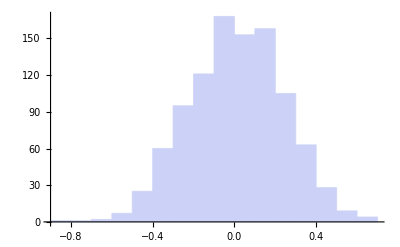

```mathematica
Histogram[ Repeat[experimentalDiff[],1000]]
```

How about over our triangles?

```mathematica
experimentalDiff[triangle3d_]:=
(meanOfNorms-normOfMeans)/.{x1:>triangle3d⟦1,1⟧,y1:>triangle3d⟦1,2⟧,z1:>triangle3d⟦1,3⟧,x2:>triangle3d⟦2,1⟧,y2:>triangle3d⟦2,2⟧,z2:>triangle3d⟦2,3⟧,x3:>triangle3d⟦3,1⟧,y3:>triangle3d⟦3,2⟧,z3:>triangle3d⟦3,3⟧,xc->cameraPosition⟦1⟧,yc->cameraPosition⟦2⟧,zc->cameraPosition⟦3⟧}
```

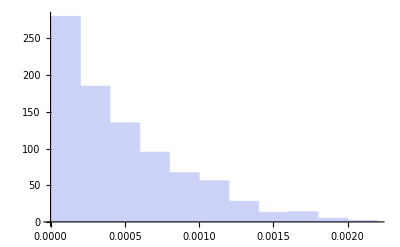

```mathematica
Histogram[experimentalDiff/@triangles3d]
```

Not such a big deal for us that we’re going to worry about it

```mathematica
(zorders=Map[
triangle3d↦normOfMeans/.{x1:>triangle3d⟦1,1⟧,y1:>triangle3d⟦1,2⟧,z1:>triangle3d⟦1,3⟧,x2:>triangle3d⟦2,1⟧,y2:>triangle3d⟦2,2⟧,z2:>triangle3d⟦2,3⟧,x3:>triangle3d⟦3,1⟧,y3:>triangle3d⟦3,2⟧,z3:>triangle3d⟦3,3⟧,xc->cameraPosition⟦1⟧,yc->cameraPosition⟦2⟧,zc->cameraPosition⟦3⟧},
triangles3d])//Take[#,5]&//MatrixForm
```

(2.77568
2.73092
2.89334
2.85281
2.99045)

```mathematica
Export["e:/LINQdoesGraphics/TEAPOT/teapotZorders2d.csv",zorders]
```

e:/LINQdoesGraphics/TEAPOT/teapotZorders2d.csv

```mathematica
triangle2dFromTriangle3d[
triangle3d_,
cameraPosition3d_,
focalLength_]:=
Map[
vertex3d↦viewportTransform[
vertex3d,
cameraPosition3d,
focalLength],
triangle3d]
```

```mathematica
(triangles2d=Map[
triangle3d↦
triangle2dFromTriangle3d[
triangle3d,
cameraPosition,
1.0],
triangles3d])//Take[#,5]&//MatrixForm
```

((-0.395791
2.11089) | (-0.419649
2.23171) | (-0.430421
2.26588)
(-0.430421
2.26588) | (-0.406518
2.14482) | (-0.395791
2.11089)
(-0.419649
2.23171) | (-0.485064
2.32945) | (-0.495961
2.36381)
(-0.495961
2.36381) | (-0.430421
2.26588) | (-0.419649
2.23171)
(-0.485064
2.32945) | (-0.582803
2.39487) | (-0.593885
2.42935))

```mathematica
RandomColor[opacity_:0.50]:=RGBColor[RandomReal[],RandomReal[],RandomReal[]]
```

```mathematica
(trianglesAndZs=MapThread[List,{triangles2d,zorders}])//Take[#,5]&//TableForm
```

-0.395791 | 2.11089
-0.419649 | 2.23171
-0.430421 | 2.26588 | 2.77568
-0.430421 | 2.26588
-0.406518 | 2.14482
-0.395791 | 2.11089 | 2.73092
-0.419649 | 2.23171
-0.485064 | 2.32945
-0.495961 | 2.36381 | 2.89334
-0.495961 | 2.36381
-0.430421 | 2.26588
-0.419649 | 2.23171 | 2.85281
-0.485064 | 2.32945
-0.582803 | 2.39487
-0.593885 | 2.42935 | 2.99045

```mathematica
(zOrderedTriangles=#⟦1⟧&/@Sort[trianglesAndZs,#1⟦2⟧>#2⟦2⟧&])//Take[#,5]&//MatrixForm
```

((-0.504304
1.81579) | (-0.623183
1.79232) | (-0.592077
1.70825)
(-0.529113
1.91804) | (-0.658912
1.89241) | (-0.623183
1.79232)
(-0.719347
1.72795) | (-0.623183
1.79232) | (-0.658912
1.89241)
(-0.623183
1.79232) | (-0.504304
1.81579) | (-0.529113
1.91804)
(-0.676713
1.65161) | (-0.592077
1.70825) | (-0.623183
1.79232))

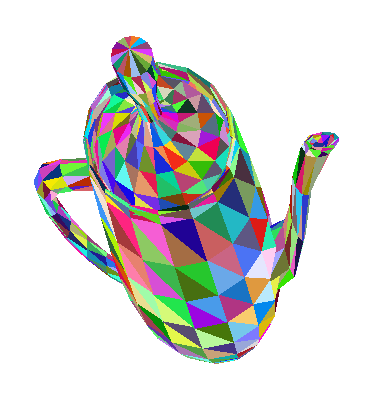

```mathematica
Graphics[{RandomColor[],Polygon[#]}&/@zOrderedTriangles]
```

```mathematica
Export[
"e:/LINQdoesGraphics/TEAPOT/teapot2d.csv",
triangles2d,
"CSV"]
```

e:/LINQdoesGraphics/TEAPOT/teapot2d.csv

```mathematica
Export[
"e:/LINQdoesGraphics/TEAPOT/zOrderedTeapot2d.csv",
zOrderedTriangles,
"CSV"]
```

e:/LINQdoesGraphics/TEAPOT/zOrderedTeapot2d.csv

## BUILT-IN Mathematica IMPORTERS

Of course, Mathematica has an importer for OFF files!

```mathematica
<<"Jacquard.m"
```

```mathematica
teapot2=Import["e:/LINQdoesGraphics/TEAPOT/teapot.off"]
```

-Graphics3D-